# Homework 30

## Problem 30.1

Consider a pancake undergoing free rotation with no external torque. Its principal moments are 0.4, 0.4, and 0.7 kg m^2. Its initial angular velocity vector is (1, 0, 5) rad/s in the body frame. Let’s calculate how the pancake behaves.

```mathematica
Quit[]
```

First, a qualitative prediction: Will the angular velocity vector remain constant in this zero-torque situation?
Write your answer here (feel free to come back later and modify it):

The angular velocity will not remain constant as as the angular velocity is not purely along a principle axis. 

Now let’s calculate the behavior and see if your answer is correct. Let:
omega0 be the initial angular velocity vector
MI be the moment of inertia tensor (written just as a 3-component vector because all the off-diagonal elements are zero)
w1[t], w2[t], w3[t] be the components of the angular velocity as expressed in body coordinates

0.4

0.4

0.7

-0.75 w3[t]

w1'[t]==-0.75 w2[t] w3[t]

w2'[t]==0.75 w1[t] w3[t]

w3'[t]==0

{w1[0]==1,w2[0]==0,w3[0]==5,w1'[0]==0,w2'[0]==0,w3'[0]==0}

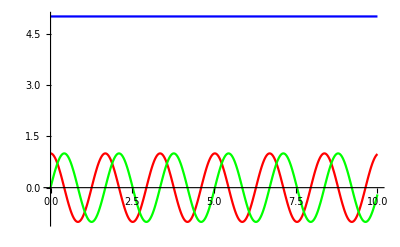

```mathematica
omega0={1, 0, 5};
lam1 = 0.4
lam2 = 0.4
lam3 = 0.7
MI={{lam1, 0, 0},{0, lam2, 0},{0, 0, lam3}};
Omegab = (lam1-lam3)*w3[t]/lam1
eq1=w1'[t] == Omegab*w2[t]
eq2=w2'[t]==-Omegab*w1[t]
eq3=w3'[t] == 0
bc={w1[0]==1, w2[0]==0, w3[0]==5, w1'[0]==0, w2'[0]==0, w3'[0]==0}
sol1=NDSolve[{eq1,eq2,eq3,bc[[1]],bc[[2]],bc[[3]]},{w1,w2,w3},{t,0,10}];
Plot[{w1[t]/.sol1,w2[t]/.sol1,w3[t]/.sol1},{t,0,10},PlotStyle->{Red,Green,Blue}]
```

You should see that one of components of the angular velocity is constant while the other two vary sinusoidally. Briefly explain what this plot means physically for the angular velocity and angular momentum of the disk as observed in the body frame.

Type your answer here (a couple of sentences should be fine):
In the body frame this means the angular velocity is conserved along the 3rd principle axis i.e. w3 because of this the 3rd component of the angular momentum L3 is also conserved in the body frame.

Now let’s compare the numerical solution with the analytical solution given in Eq. 10.94.

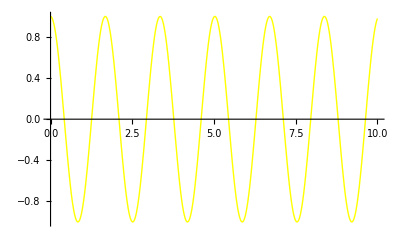

```mathematica
Omegab=Omegab ;
Plot[{w1[t]/.sol1,omega0[[1]]*Cos[Omegab*t]},{t,0,10},PlotStyle->{{Yellow,Thick},{Blue,Dashed}}]
```

The two curves should agree.

## Written Problems

-Graphics-